## Image processing- RGB glucose

### import data

```mathematica
ClearAll;
glucose1=Import["/Users/naomi/Documents/naomi/tissue microfluidics/photos 2:12:13/glucose 50mM.jpg"];
backgroundimage=Import["/Users/naomi/Documents/naomi/tissue microfluidics/photos 2:12:13/glucose 50mM edit.jpg"];
```

#### crop to region of interest

```mathematica
croppedglucose1=ImageTake[glucose1,{1300,1700},{1550,1850}];
croppedbackground=ImageTake[backgroundimage,{1300,1700},{1550,1850}];
```

#### subtract the background

```mathematica
differenceimage=ImageDifference[croppedglucose1,croppedbackground];
Show[differenceimage, ImageSize->Small]
```

-Graphics-

#### Total pixel intensity (RGB)

```mathematica
intensity50mM=Total[ImageData[differenceimage],2]
```

{20584.7,28284.,35499.4}

### second sample

```mathematica
glucose2=
ImageTake[Import["/Users/naomi/Documents/naomi/tissue microfluidics/photos 2:12:13/glucose 50mM less bright.jpg"],{1300,1700},{1550,1850}];
```

```mathematica
glucose2lessbg=ImageDifference[glucose2, croppedbackground];
Show[glucose2lessbg, ImageSize->Small]
```

-Graphics-

```mathematica
intensitysample2=Total[ImageData[glucose2lessbg],2]
```

{17415.8,23385.4,27921.1}

### comparison of two samples

```mathematica
intensity50mM-intensitysample2
```

```mathematica
{3168.8352941176636,4898.568627450964,7578.313725490119}
```

{3168.84,4898.57,7578.31}

```mathematica
Clear[arrayglucose]
```

```mathematica
conc1=50;
conc2=25;
arrayglucose={};
AppendTo[arrayglucose,{intensity50mM,conc1}];
arrayglucose
AppendTo[arrayglucose,{intensitysample2,conc2}];
arrayglucose
```

{{{20584.7,28284.,35499.4},50}}

{{{20584.7,28284.,35499.4},50},{{17415.8,23385.4,27921.1},25}}

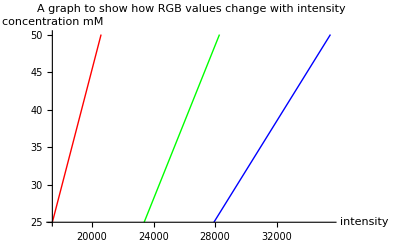

```mathematica
ListLinePlot[listall,PlotStyle->{Red,Green,Blue}, AxesLabel->{"intensity","concentration mM"},PlotLabel->"A graph to show how RGB values change with intensity"]
```

```mathematica
listall=Table[{arrayglucose[[i]][[1]][[j]],arrayglucose[[i]][[2]]},{j,3},{i,Length[arrayglucose]}]
```

{{{20584.7,50},{17415.8,25}},{{28284.,50},{23385.4,25}},{{35499.4,50},{27921.1,25}}}